```mathematica
<<Utilities`CleanSlate`
ClearAll["Global`*"]
LHS = Assuming[{c>R>0},∫_R^c n  B(((Eo c)/(No r))^2-(Eo/No)^2)ⅆr];
RHS = Log[Q];
Sol1 =  Simplify[Solve[LHS==RHS,c]];
c = Normal[c/.Sol1[[2]]];
Ec[R_] = Simplify[n/No Eo c/R];
Vc[R_] = Simplify[n/No Eo c Log[R2/R]];
Sol2 = Flatten[Solve[D[Vc[R], R]==0,R]];
Vmin = Simplify[Vc[R]/.Sol2];
Rmin = R/.Sol2;
(*Rmin =Simplify[Normal[Series[Rmin,{R2,∞,1}]]];*)
Print["Ec[R] = ",Ec[R], " (V/m)"];
Print["Vc[R] = ",Vc[R], " (V)"];
Print["Rmin = ",Rmin, " (m)"];
Print["Vmin = ",Vmin, " (V)"];
```

Solve::dinv: The expression (R2/R)^No\ √Log[Q]/2\ √B\ Eo\ √n\ √R involves unknowns in more than one argument, so inverse functions cannot be used.

General::stop: Further output of Solve :: "dinv" will be suppressed during this calculation.

ReplaceAll::reps: {Solve[-n\ (Eo\ R + Power[« 2 »]\ Power[« 2 »]\ No\ Power[« 2 »]\ Power[« 2 »])/No\ R + n\ (Eo + 1/2\ « 4 »\ Power[« 2 »])\ Log[Power[« 2 »]\ R2]/No == 0, R]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Ec[R] = (Eo n)/No+(√n √Log[Q])/(√B √R) (V/m)

Vc[R] = (n (Eo R+(No √R √Log[Q])/(√B √n)) Log[R2/R])/No (V)

Rmin = R/.Solve[-(n (Eo R+(No √R √Log[Q])/(√B √n)))/(No R)+(n (Eo+(No √Log[Q])/(2 √B √n √R)) Log[R2/R])/No==0,R] (m)

Vmin = (n (Eo R+(No √R √Log[Q])/(√B √n)) Log[R2/R])/No/.Solve[(√n No √Log[Q] (-2+Log[R2/R])+2 √B Eo n √R (-1+Log[R2/R]))/(√B No √R)==0,R] (V)

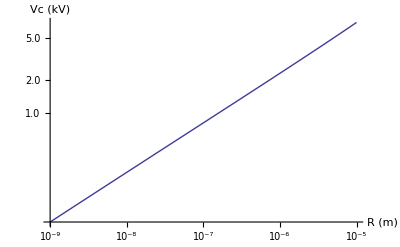

```mathematica
B = 2.08 10^16;
Q = 10^4;
p= 101325;
δ = 1;
No = 2.688 10^19 10^6;
n = No;
Eo = 31 10^5;
R2 = 1000;
LogLogPlot[Vc[R]/1000, {R,10^-9,10^-5}, AxesLabel-> {"R (m)", "Vc (kV)"}]
```